```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
m=2;
P=2^m;
T=100P-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
(Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧-nM⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
WM=nM⟦t⟧*Price⟦t⟧;
ΔcM⟦t-1⟧=+A⟦t-1⟧*Price⟦t⟧;
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

{3.33919,Null}

```mathematica
Tinfor
```

{55,47,47,52}

```mathematica
T
```

400

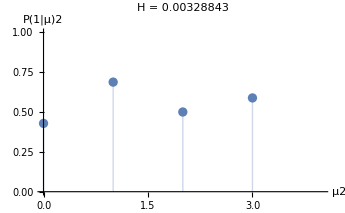

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,50P,100P-1},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,50P,100P-1}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(50P)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n]]]
```

```mathematica
BScollect;
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

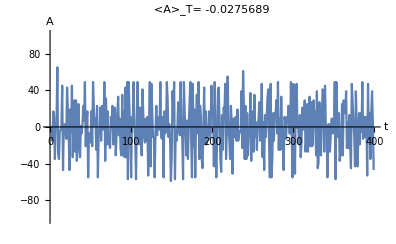

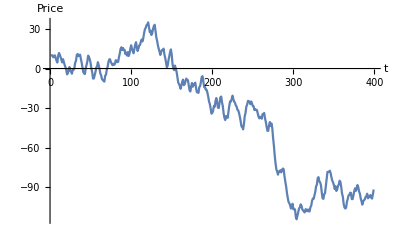

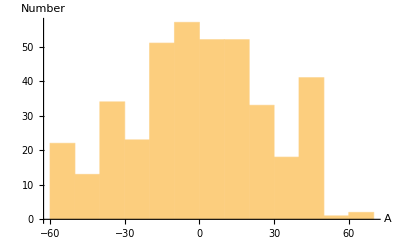

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->"<A>_T= "<>ToString[N[Mean[A⟦t1+1;;t2⟧]]]]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","Price"},PlotRange->Automatic,Joined->True]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

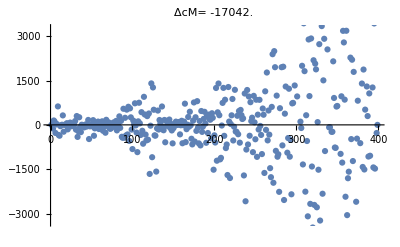

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦3;;T⟧]]]]
```

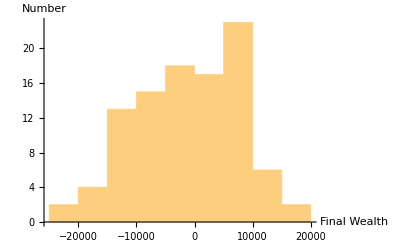

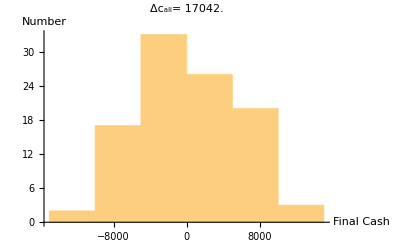

```mathematica
f4=Histogram[W⟦2;;n⟧-190,Automatic,AxesLabel->{"Final Wealth","Number"}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
c
```

{51.8402,5802.78,5558.59,-691.361,-4154.69,8218.14,-5203.77,-8018.14,2988.2,5608.05,-5853.93,2138.05,6007.55,3194.97,3704.14,7362.9,-12029.1,11587.2,3392.88,-2142.62,-6364.98,1581.91,11305.3,-631.755,-3320.75,8044.81,5465.36,7470.07,-6280.1,5615.61,-10543.3,7393.45,-7774.75,786.973,-3427.12,-2613.47,1011.16,-695.636,-2900.05,4221.65,-2930.3,5813.92,3272.39,-7736.45,805.087,4189.91,-1604.9,-1952.77,-647.674,-1363.61,-3851.41,190.146,8948.8,-7175.14,-523.396,-4578.68,7236.63,2402.83,-1924.61,-1912.77,5528.84,844.885,5405.95,-6187.47,-5110.33,-3828.52,7187.57,-2423.62,-1841.62,2335.26,-285.578,-3863.24,-1449.67,1051.75,7501.61,-1843.51,2099.44,454.336,11190.4,2109.09,3291.79,9554.78,-8018.14,-6112.63,-3320.75,-5182.77,-4915.8,-4915.8,2658.25,-4751.82,-5904.17,-3346.42,-5012.22,3406.42,5040.77,2688.79,3194.97,-4816.,-3862.15,-866.183,6931.35}